## Shutter speed ramp required for constant image brightness

Parameters used throughout:

```mathematica
(* Environment brightness function parameters *)
min=1;
max=100;
rate=1/3;

(* Seconds between end of one frame and start of next *)
pause=0.5;

(* Timelapse parameters *)
frames=900;
elapsed=4 60 60; (* sec *)

(* Camera settings *)
iso=160;
area=0.00008658;
```

```mathematica
SetOptions[{Plot,ListPlot},ImageSize->{400,220}];
```

Ambient brightness vs. sun zenith angle past sunset:

```mathematica
BrightnessWithAngle[θ_,min_,max_,rate_]:=(max-min)Exp[-rate θ]+min
```

Sun zenith angle in degrees vs. local time in hours:

```mathematica
AngleWithTime[sec_]:=(360 sec)/86400 (* Assume earth is pointlike compared to distance to sun  *)
```

Ambient brightness vs. time

```mathematica
BrightnessWithTime[sec_?NumericQ,min_,max_,rate_]:=BrightnessWithAngle[AngleWithTime[sec],min,max,rate]
```

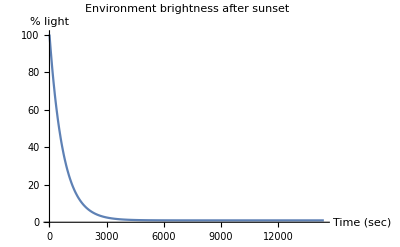

```mathematica
Plot[BrightnessWithTime[t,min,max,rate],{t,0,elapsed},AxesOrigin->{0,0},AxesLabel->{"Time (sec)","% light"},PlotLabel->"Environment brightness after sunset",LabelStyle->{GrayLevel[0]},PlotRange->{0,100}]
```

Relative shutter speed vs. time function (continuous approximation)

```mathematica
ExposureAtTimeT[T_,min_,max_,rate_,iso_,area_]:=x/.(FindRoot[NIntegrate[BrightnessWithTime[t,min,max,rate],{t,T,T+x}]==1/(iso area),{x,1}]//Quiet)
```

Compute each frame’s relative exposure time

```mathematica
EXPTIMES={};curtime=0;
Do[curr=ExposureAtTimeT[curtime,min,max,rate,iso,area];
AppendTo[EXPTIMES,curr];
curtime+=(curr+pause);,
frames]
```

Check that the elementwise product of EXPTIMES and corresponding brightness (aka the image brightness) is a constant.

```mathematica
CHK={};curfr=1;curt=0;
Do[
curexp=EXPTIMES[[curfr]];
avgbright=1/curexp NIntegrate[BrightnessWithTime[t,min,max,rate],{t,curt,curt+curexp}];
prod=iso area curexp avgbright;
AppendTo[CHK,prod];
curt+=(curexp+pause);
curfr++;,
frames]
Print["μ = ",Mean[CHK],", σ^2 = ",Variance[CHK]]
```

μ = 1., σ^2 = 3.08197×10^-28

Scale all exposure times such that the total elapsed time equals  “elapsed”

```mathematica
scale=s/.Solve[(s(Total[EXPTIMES])+(frames-1)pause)==elapsed,s];
SCALEDEXPTIMES=scale[[1]]EXPTIMES;
```

Plot scaled exposure times with elapsed time

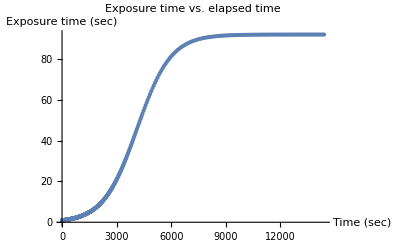

```mathematica
frtime[i_]:=(SCALEDEXPTIMES[[i]]+pause)
times=Accumulate[Map[frtime,Range[1,frames]]];
ListPlot[Transpose[{times,SCALEDEXPTIMES}],AxesOrigin->{0,0},AxesLabel->{"Time (sec)","Exposure time (sec)"},PlotLabel->"Exposure time vs. elapsed time",LabelStyle->{GrayLevel[0]},PlotRange->{{0,elapsed},{0,Max[SCALEDEXPTIMES]}}]
```

Plot scaled exposure times with frame number

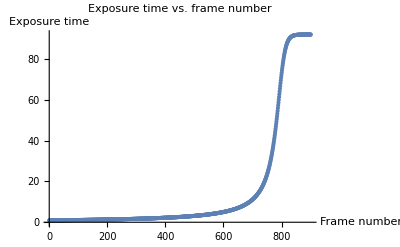

```mathematica
ListPlot[SCALEDEXPTIMES,AxesOrigin->{1,0},AxesLabel->{"Frame number","Exposure time"},PlotLabel->"Exposure time vs. frame number",LabelStyle->{GrayLevel[0]},PlotRange->{{1,frames},{0,Max[SCALEDEXPTIMES]}}]
```